# Universal Quantum Computation: Demonstration

Here we provide a simple demonstration that any arbitrary unitary operation can be implemented by combining CNOT gate and single-qubit rotations.

TwoLevelDecomposition | returns a list of two-level unitary operators.
TwoLevelU | represents the two-level unitary operators.
GrayTwoLevelU | rewrites the two-level unitary operators in terms of CNOT and controlled-U gates.

Some functions conveniently used for the demonstration of universal quantum computation.

### Step 1. Decomposition into two-Level unitary operations

We first decompose the unitary operation into two-level unitary operations, that is, unitary operators acting only on a two-dimensional subspace.

Gray is a supplementary package and is not loaded by default when the Q3 App is loaded. You need to load it manually.

```mathematica
<<Q3`Gray`
```

```mathematica
Let[Qubit,S]
```

Consider a 2^n×2^n unitary matrix.

```mathematica
n=2;
mat=RandomUnitary[2^n];
mat//MatrixForm
```

(-0.327811-0.367822 ⅈ | -0.0231144-0.592851 ⅈ | 0.0782758+0.354026 ⅈ | 0.311278-0.420575 ⅈ
-0.205364-0.374427 ⅈ | 0.390691+0.00352709 ⅈ | 0.70506-0.133672 ⅈ | -0.25811+0.288755 ⅈ
-0.39737+0.216532 ⅈ | -0.0946958+0.440907 ⅈ | 0.22208+0.331459 ⅈ | 0.600368+0.268736 ⅈ
-0.608056+0.0188498 ⅈ | 0.464418+0.276208 ⅈ | -0.437603+0.0536657 ⅈ | -0.307544-0.221309 ⅈ)

This is an explicit operator expression of the unitary transformation.

```mathematica
nn=Range[n];
SS=S[nn,None];
opU=QuissoExpression[mat,SS]
```

(-0.00564614-0.0635361 ⅈ)+(0.0783965-0.0236227 ⅈ) S_1^x S_2^x-(0.0337882-0.0298948 ⅈ) S_1^x S_2^y-(0.131351-0.00139878 ⅈ) S_1^x S_2^z+(0.253501+0.429773 ⅈ) S_1^y S_2^x+(0.226786+0.17724 ⅈ) S_1^y S_2^y-(0.0312366-0.299543 ⅈ) S_1^y S_2^z-(0.0978109+0.32242 ⅈ) S_1^z S_2^x+(0.108374-0.21393 ⅈ) S_1^z S_2^y-(0.312032+0.231029 ⅈ) S_1^z S_2^z-(0.0281964-0.28388 ⅈ) S_1^x-(0.0375104+0.0617205 ⅈ) S_1^y+(0.0370861-0.118611 ⅈ) S_1^z-(0.0164285+0.161219 ⅈ) S_2^x+(0.000838523+0.305055 ⅈ) S_2^y-(0.0472196-0.0453547 ⅈ) S_2^z

Here is a two-level decomposition, where the results are in terms of TwoLevelUpaclet:Q3/ref/TwoLevelU.

```mathematica
mm=TwoLevelDecomposition[mat]
```

{TwoLevelU[{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.0886224-0.996065 ⅈ}},{3,4},4],TwoLevelU[{{-0.524092+0.285585 ⅈ,0.0958354-0.796608 ⅈ},{-0.0958354-0.796608 ⅈ,-0.524092-0.285585 ⅈ}},{3,4},4],TwoLevelU[{{0.235997+0.430277 ⅈ,0.871302},{-0.871302,0.235997-0.430277 ⅈ}},{2,3},4],TwoLevelU[{{-0.661115+0.24858 ⅈ,-0.51506+0.485642 ⅈ},{0.51506+0.485642 ⅈ,-0.661115-0.24858 ⅈ}},{3,4},4],TwoLevelU[{{-0.327811-0.367822 ⅈ,0.870199},{-0.870199,-0.327811+0.367822 ⅈ}},{1,2},4],TwoLevelU[{{-0.0265622-0.681282 ⅈ,0.731539},{-0.731539,-0.0265622+0.681282 ⅈ}},{2,3},4],TwoLevelU[{{0.122962+0.556134 ⅈ,0.488982-0.660675 ⅈ},{-0.488982-0.660675 ⅈ,0.122962-0.556134 ⅈ}},{3,4},4]}

You can convert the above results to more human readable full matrix form by means of Matrixpaclet:Q3/ref/Matrix.

```mathematica
MatrixForm/@Matrix/@mm
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1.+0. ⅈ | 0
0 | 0 | 0 | 0.0886224-0.996065 ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.524092+0.285585 ⅈ | 0.0958354-0.796608 ⅈ
0 | 0 | -0.0958354-0.796608 ⅈ | -0.524092-0.285585 ⅈ),(1 | 0 | 0 | 0
0 | 0.235997+0.430277 ⅈ | 0.871302 | 0
0 | -0.871302 | 0.235997-0.430277 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.661115+0.24858 ⅈ | -0.51506+0.485642 ⅈ
0 | 0 | 0.51506+0.485642 ⅈ | -0.661115-0.24858 ⅈ),(-0.327811-0.367822 ⅈ | 0.870199 | 0 | 0
-0.870199 | -0.327811+0.367822 ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -0.0265622-0.681282 ⅈ | 0.731539 | 0
0 | -0.731539 | -0.0265622+0.681282 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.122962+0.556134 ⅈ | 0.488982-0.660675 ⅈ
0 | 0 | -0.488982-0.660675 ⅈ | 0.122962-0.556134 ⅈ)}

Check the decomposition with the original matrix.

```mathematica
new=Dot@@Matrix/@mm;
mat-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Step 2. Rewriting two-level unitary operators to elementary gates.

Now we rewrite each two-level unitary operator in terms of elementary gates, that is, in a combination of CNOT gates and one controlled-U gate.

GrayTwoLevelUpaclet:Q3/ref/GrayTwoLevelU does the job.

```mathematica
gates=Catenate[GrayTwoLevelU[#,S@nn]&/@mm]
```

{ControlledU[{S_1},(0.544311-0.498033 ⅈ)+(0.455689+0.498033 ⅈ) S_2^z,Label→U],ControlledU[{S_1},(-0.524092+0. ⅈ)-(0.+0.796608 ⅈ) S_2^x+(0.+0.0958354 ⅈ) S_2^y+(0.+0.285585 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.235997+0. ⅈ)-(0.+0.871302 ⅈ) S_2^y-(0.+0.430277 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.661115+0. ⅈ)+(0.+0.485642 ⅈ) S_2^x-(0.+0.51506 ⅈ) S_2^y+(0.+0.24858 ⅈ) S_2^z,Label→U],{S_1^x},ControlledU[{S_1},(-0.327811+0. ⅈ)+(0.+0.870199 ⅈ) S_2^y-(0.+0.367822 ⅈ) S_2^z,Label→U],{S_1^x},CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.0265622+0. ⅈ)-(0.+0.731539 ⅈ) S_2^y+(0.+0.681282 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.122962+0. ⅈ)-(0.+0.660675 ⅈ) S_2^x+(0.+0.488982 ⅈ) S_2^y+(0.+0.556134 ⅈ) S_2^z,Label→U]}

Here is a quantum circuit model of the decomposition. Here controlled-U gates are all labeled by the same character "U" but in fact they are different operators. Also do not forget to reverse the order of the elementary gates in the quantum circuit model.

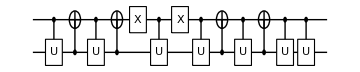

```mathematica
qc=QuissoCircuit[Reverse@gates]
```

```mathematica
new=QuissoExpression[qc]
```

(-0.00564614-0.0635361 ⅈ)+(0.0783965-0.0236227 ⅈ) S_1^x S_2^x-(0.0337882-0.0298948 ⅈ) S_1^x S_2^y-(0.131351-0.00139878 ⅈ) S_1^x S_2^z+(0.253501+0.429773 ⅈ) S_1^y S_2^x+(0.226786+0.17724 ⅈ) S_1^y S_2^y-(0.0312366-0.299543 ⅈ) S_1^y S_2^z-(0.0978109+0.32242 ⅈ) S_1^z S_2^x+(0.108374-0.21393 ⅈ) S_1^z S_2^y-(0.312032+0.231029 ⅈ) S_1^z S_2^z-(0.0281964-0.28388 ⅈ) S_1^x-(0.0375104+0.0617205 ⅈ) S_1^y+(0.0370861-0.118611 ⅈ) S_1^z-(0.0164285+0.161219 ⅈ) S_2^x+(0.000838523+0.305055 ⅈ) S_2^y-(0.0472196-0.0453547 ⅈ) S_2^z

```mathematica
new-opU//Garner//Chop
```

0

Related Guides

Quisso Package Guide

Related Tutorials

Quisso: Quick Start

QuissoCircuit Usage Examples

Quantum Fourier Transform

Quantum Teleportation

Related Wolfram Education Group Courses

An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/

The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/